```mathematica
f[x_]:= 2 *x^2;
g[x_]:= 3 * x^2;
f2[x_]:= 2 * x^4;
g2[x_]:= 3* x^4;
```

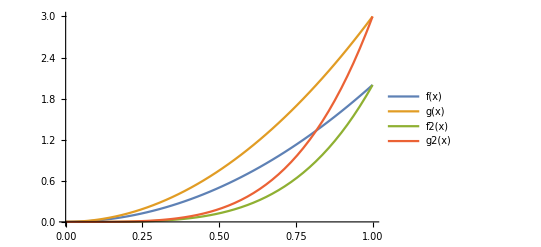

```mathematica
Plot[{f[x], g[x], f2[x], g2[x]}, {x,0, 1}, PlotLegends->"Expressions"]
```

```mathematica
c= 0;
```

```mathematica
f[h_] := (Sin[c + h] - Sin[c-h]) / (2*h)
g[h_] := (Sin[c+h] - Sin[c]) / h
f5[h_]:= (-Sin[c +2*h] + 8*Sin[c+h] - 8*Sin[c-h] + Sin[c-2*h])/ (12 *h)
```

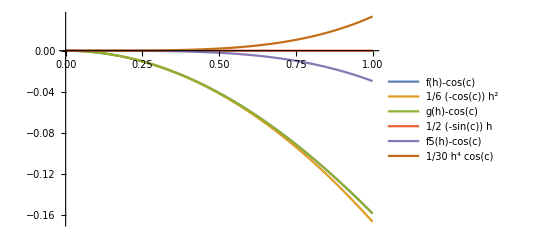

```mathematica
Plot[{f[h] - Cos[c],-Cos[c]* h^2 / 6, g[h]-Cos[c], -Sin[c]* h / 2, f5[h] - Cos[c], h^4 * Cos[c]/30 },{h,0, 1}, PlotLegends->"Expressions"]
```

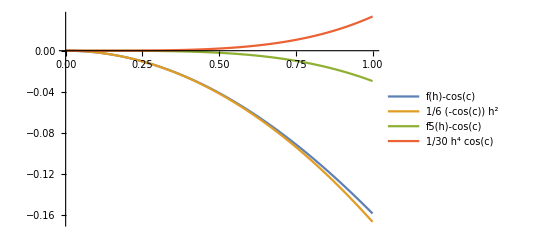

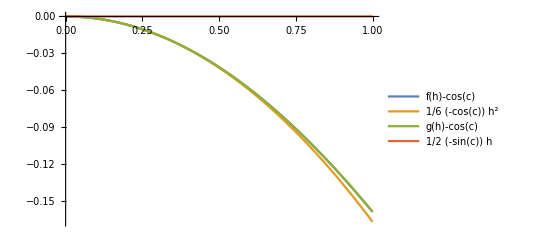

```mathematica
Plot[{f[h] - Cos[c],-Cos[c]* h^2 / 6,  f5[h] - Cos[c], h^4 * Cos[c]/30 },{h,0, 1}, PlotLegends->"Expressions"]

Plot[{f[h] - Cos[c],-Cos[c]* h^2 / 6, g[h]-Cos[c], -Sin[c]* h / 2 },{h,0, 1}, PlotLegends->"Expressions"]
```



```mathematica
Plot[Sin[x], {x, 0, 10}, PlotLegends->"Expressions"]
```

```mathematica
testfun[x_] := Sin[x]
testfunderiv[x_]  := Cos[x]
```

```mathematica
Plot[testfun[x], {x, 0, 10}, PlotLegends->"Expressions"]
```

-Graphics-

```mathematica
derivative[h_, x_]:=  (testfun[x+h] - testfun[x]) / h
deriv2point[h_,x_]:= (testfun[x+h] - testfun[x-h])/ (2*h)
deriv5point[h_,x_]:=(-testfun[x+ 2*h]  + 8*testfun[x+h] - 8*testfun[x-h]+testfun[x-2*h] )/ (12*h)
```

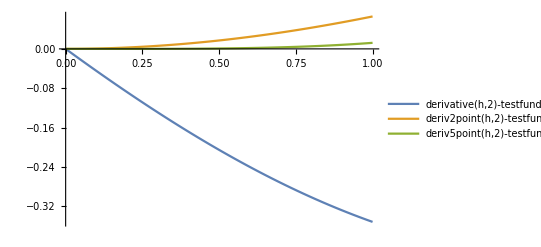

```mathematica
Plot[{derivative[h,2] - testfunderiv[2], deriv2point[h,2] - testfunderiv[2], deriv5point[h,2] - testfunderiv[2]}, {h,0,1}, PlotLegends->"Expressions"]
```